# Plots Across Parameter Runs

## Data Selection

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
plotsDir= "kl_div_plots";
dataDir = "mlflow_data";
```

```mathematica
(*Set the name of the experiment.*)
experiments =FileNameTake/@(FileNames[All, dataDir]);
experimentName =.;
PopupMenu[Dynamic[experimentName],experiments]
```

```mathematica
(*Get the experiment directory and the names of all the runs in that directory.*)
experimentDir=FileNameJoin[{dataDir, experimentName}];
runDirs = FileNames[All, experimentDir];
runNames = FileNameTake/@runDirs;

(*Select which metric to plot.*)
availableMetrics = {"kl", "reco", "loss","rate_0.3", "rate_1", "z_mean_squared_rate0.3", "loss_reco_full_rate0.3","loss_total_full_rate0.3", "loss_kl_full_rate0.3", "cap"};
desiredMetric=availableMetrics[[1]];
PopupMenu[Dynamic[desiredMetric, (desiredMetric=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"datasetSelection"}}])&
],availableMetrics]
```

```mathematica
datasets = Intersection[FileNameTake/@Flatten@Table[FileNames[All, runDirs[[i]]],{i, 1, Length@runDirs}]];
datasets = If[desiredMetric == "cap", Select[datasets, StringContainsQ[desiredMetric]],Select[datasets, StringContainsQ[desiredMetric <> "."]]];
desiredDataset=datasets[[2]];
PopupMenu[Dynamic[desiredDataset, (desiredDataset=#;
SelectionMove[EvaluationNotebook[],Before,Notebook];
Do[NotebookFind[EvaluationNotebook[],tag,All,CellTags];
SelectionEvaluate[EvaluationNotebook[]],{tag,{"labels","importData","plotGrid"}}])&
],datasets]
```

## Metadata

```mathematica
(*Extract parameters from run names. Will be used as labels for the plots.*)
processRunName[runName_] := (
name = {};
splitRunName = StringSplit[runName,"_"];
lrName = Select[splitRunName, StringContainsQ["lr"]];
alphaName =Select[splitRunName, StringContainsQ["alpha"]];
name =Append[name, "η = "<>Flatten@StringCases[lrName,NumberString] <> ", " <> "α = "<>Flatten@StringCases[alphaName,NumberString]];
name
)
runLabels =processRunName/@runNames;
Style["List of the runs that will be plotted: ", "Subsection"]
Framed[Pane[Column[runLabels], {200, 150}, Scrollbars->True]]
```

List of the runs that will be plotted:

{η = 0.001, α = 0.2}
{η = 0.001, α = 0.4}
{η = 0.001, α = 0.7}
{η = 0.001, α = 0.8}
{η = 0.001, α = 0.9}

## Import Data

```mathematica
(*Get the data to plot from all the runs inside the experiment.*)
dataPaths = Select[FileNames[All, runDirs],StringContainsQ[desiredDataset]];
plotData = Table[BinaryReadList[dataPaths[[i]], "Real32"], {i, 1, Length@dataPaths}];
plotData // Dimensions
```

{5,100}

```mathematica
(*Restrict values to be between 0 and 1, for better plotting visibility if the data is kl divergence related.*)
If[desiredMetric == "kl",plotData =Clip[plotData, {0,3}]];
If[desiredMetric == "loss",plotData =Clip[plotData, {0,3}]];
```

```mathematica
Style["Plotting data for " <> desiredDataset, "Title"]
```

Plotting data for cap_background1.dat

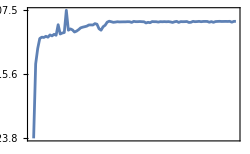
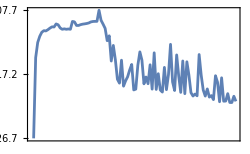
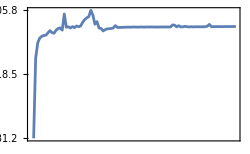
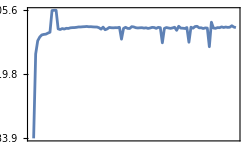
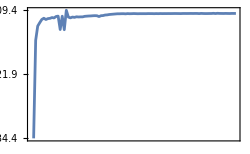
|  | η = 0.001
 α = 0.2 | -Graphics-
 α = 0.4 | -Graphics-
 α = 0.7 | -Graphics-
 α = 0.8 | -Graphics-
 α = 0.9 | -Graphics-
 | Epochs ∈ [0, 100]cap_background1

```mathematica
makePlot[row_]:=ListLinePlot[row,PlotStyle->{Medium},Axes->False,Frame->True,FrameTicks->{{{{Min@Select[row, NumberQ],NumberForm[N[Min@Select[row, NumberQ]], {5, 1}]},{(Min@Select[row, NumberQ]+(Max@Select[row, NumberQ] - Min@Select[row, NumberQ])/2),NumberForm[N[Min@Select[row, NumberQ]+(Max@Select[row, NumberQ] - Min@Select[row, NumberQ])/2],{5,1}]}, {Max@Select[row, NumberQ],NumberForm[N[Max@Select[row, NumberQ]],{5,1}]}}, None}, {None, None}},FrameTicksStyle->Directive[11, FontWeight->"Plain"],PlotRange->All,ImageSize->250,PlotLabel->None];
plots = makePlot /@ plotData;
learningRates = DeleteDuplicates[StringSplit[#[[1]],","][[1]] &/@runLabels];
alphas = DeleteDuplicates[StringSplit[#[[1]],","][[2]] &/@runLabels];

(*Group the plots in terms of the same learning rate, varying alpha, and then transpose to have alpha on the y-axis and learning rate on the x axis.*)
grid=Partition[plots,Length@alphas];
grid = Transpose[(grid)];

(*Add row labels to each row*)
rowLabels=alphas;
rowsWithLabels=MapThread[Prepend,{grid,rowLabels}];
(*Add column labels at the top,and a blank cell at top-left*)
colLabels=learningRates;
fullGrid=Prepend[rowsWithLabels,Prepend[colLabels,""]];

fullGridWithAxes=Grid[{{"",Grid[fullGrid,Spacings->{1,1},Alignment->Center]},{"",Style["Epochs ∈ [0, 100]",FontWeight->"SemiBold",24, Gray]}},Spacings->{1,2}];
yLabel=Style[Rotate[FileBaseName@desiredDataset,90 Degree],FontWeight->"SemiBold",24,Gray];

Labeled[fullGridWithAxes,yLabel,Left,LabelStyle->{FontSize->24},Spacings->{1,2}]
```

```mathematica
Export["run_grids/" <>FileBaseName@desiredDataset <> ".png",%]
```

run_grids/cap_background1.png

# Dynamic Plot

```mathematica
DynamicModule[{data,labels,groups, groupKeys, groupSelection, lineSelection = {}, hovered=None},
	data=plotData;
	labels=runLabels;
	
	groups=AssociationThread[labels->Table["Group "<> StringSplit[labels[[i]][[1]],","][[2]],{i,45}]];
	(*groups=AssociationThread[labels->Table["Group "<> StringSplit[labels[[i]][[1]],","][[1]],{i,45}]];*)
	groupKeys=DeleteDuplicates[Values[groups]];
	groupSelection={First[groupKeys]};
	
	(*Color function for selected lines*)
	colors=ColorData[97,"ColorList"];
	colorFunc=Function[i,colors[[Mod[i-1,Length[colors]]+1]]];
	
	Column[
	{
	Style["Select groups to show:",Bold],
	CheckboxBar[Dynamic[groupSelection],groupKeys],
	Button["Refresh",(groupSelection={};
	lineSelection={};
	hovered=None;),ImageSize->Medium],
	Dynamic[
	Module[{visibleLines,selectedIndices,selectedLabels,plot,overlay,selectedColors,legend},
	visibleLines=Union[Select[labels,MemberQ[groupSelection,groups[#]]&],lineSelection];
	selectedIndices=Flatten@Position[labels,_?(MemberQ[visibleLines,#]&)];
	selectedLabels=labels[[selectedIndices]];
	(*Assign colors to selected lines that are also selected*)
	selectedColors=AssociationThread[lineSelection->Table[colorFunc[i],{i,Length[lineSelection]}]];
	
	(*Plot the data*)
	plot=ListLinePlot[
	data[[selectedIndices]],
	PlotStyle->MapIndexed[Module[{lbl=labels[[#]],idx=First[#2]},Which[hovered===idx,{Thick,Red},MemberQ[lineSelection,lbl],{Thickness[0.0025],selectedColors[lbl], Opacity[0.7]},True,{Thickness[0.0015],Gray, Opacity[0.5]}]]&,selectedIndices],
	PlotRange->All,
	Axes->False,
	Frame->True,
	FrameTicksStyle->Directive[20],
	FrameLabel->{Style["Epochs\n", FontSize->24, Bold], Style[desiredMetric, FontSize->24, Bold]},
	ImageSize->{1800,1200},
	ImagePadding->120,
	PlotLegends->None
	];
	
	(*Legend placed top right inside plot*)
	legend=If[lineSelection==={},"",SwatchLegend[Values[selectedColors],Flatten@Keys[selectedColors],LegendMarkerSize->20, LabelStyle->Directive[20]]];
	overlay=Graphics[
	MapIndexed[
	With[
	{idx=First[#2],lbl=labels[[selectedIndices[[First[#2]]]]]},
	EventHandler[
	Tooltip[Invisible@Line[Transpose[{Range[Length[#1]],#1}]],lbl[[1]], TooltipStyle->Directive[16,Red, Bold]],
	{
	"MouseEntered":>(hovered=idx),
	"MouseExited":>(hovered=None),
	"MouseClicked":>(
	If[
	MemberQ[lineSelection,lbl],
	lineSelection=DeleteCases[lineSelection,lbl],
	AppendTo[lineSelection,lbl]             
	]
	)
	}
	]
	]&,data[[selectedIndices]]]
	];
	Show[plot,overlay,Epilog->Inset[legend,Scaled[{0.98,0.98}],{Right,Top}]]
	]
	]
	}]
	]
```